# Script for IRS vs BoB comparison 1:1 Mass ratio

## to accompany https://arxiv.org/abs/2205.14742

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=$MachinePrecision; (* $MachinePrecision;*)
```

Initial and final parameters

Tune to SXS 0746

```mathematica
χ1=0.577899456899;
χ2=0.797826951453;
χfSXS=0.880726115;
MfSXS=0.918682416261;
```

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf=0.8805889975382539(*mean final spin for nonspinning individual BSs in the binary *)
```

0.880589

```mathematica
Mf=0.9223376556229705(*mean final mass for nonspinning individual BSs in the binary *)
```

0.922338

Our fit: the mean value for equal non-spinning binaries from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM =0.6566451157454446(*0.6460523662254356*);
QQNM=5.003059966404495 (*4.796806396786768*);
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM(*15.144152677226*)
```

0.711936

14.0548

McWilliams fits

```mathematica
ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366)
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.211823

0.646052

PN fits

```mathematica
rISCO = 2.4474682518147417
```

2.44747

```mathematica
MfωISCO = Simplify[1/(rISCO^(3/2)+χf)]
```

0.212337

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

take the initial values from the i3PN nspiral for ti = tISCO = tLR

Values taken directly from EccInsMerger_q1e0001. For this spin, rISCO=3.45425.

```mathematica
Ω3OrbPNISCO = 0.075297 ;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
```

Now we can implement the BoB

```mathematica
Ωi =MfωISCO/2
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM=ωQNM/2
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

0.106168

0.355968

-44.3562

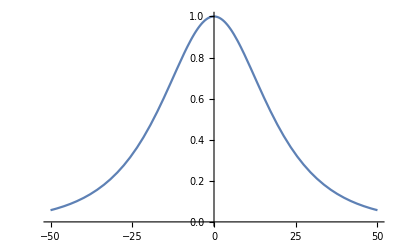

```mathematica
Ap=1;(*1.068*(1-Mf)^0.8918;*)
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00797903

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

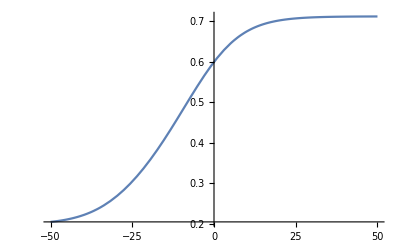

```mathematica
Plot[ωBoB[t],{t,-50,50}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.355968

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.0995333

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

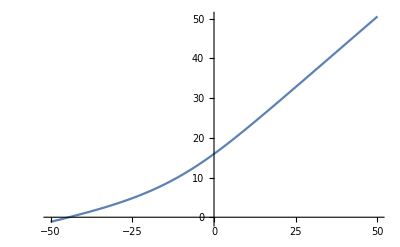

```mathematica
Plot[ϕBoB[t],{t,-50,50}]
```

```mathematica
AmpBoB[t_]:=ψ4[t]/ωBoB[t]^2
```

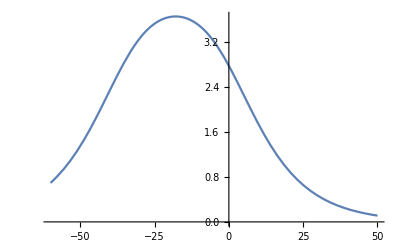

```mathematica
Plot[AmpBoB[t],{t,-60,50}]
```

```mathematica
MaxAmpBoB=FindMaxValue[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

3.65979

```mathematica
tpBoB = First@FindArgMax[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

-17.9107

```mathematica
hBoB[t_]:=-AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

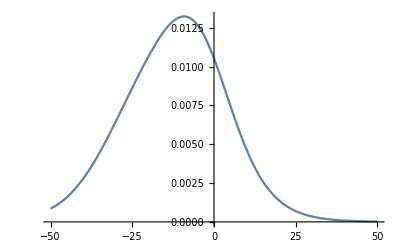

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
tfBoB=t/.FindRoot[ωBoB''[t]==0,{t,-20,10}]
```

-9.17457

Let’s build the strains

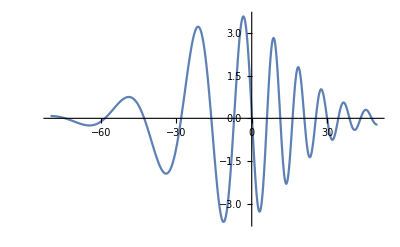

```mathematica
Plot[Re[hBoB[t+tfBoB]],{t,-80,50}]
```

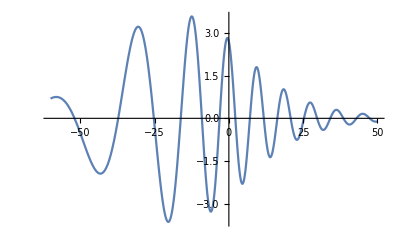

```mathematica
Plot[Re[hBoB[t]],{t,-60,50}]
```

```mathematica
MaxRehBoB = FindMaxValue[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

3.58454

```mathematica
thBoB = First@FindArgMax[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

-12.4865

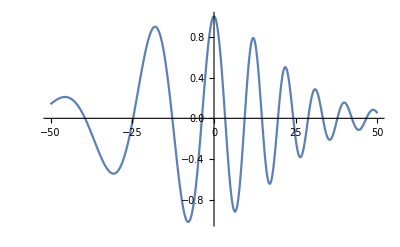

```mathematica
Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-50,50}]
```

```mathematica
Δtf = tfBoB-tpBoB
Δtp = thBoB-tpBoB
```

8.73614

5.4242

Now we upload the SXS BBH:0180 data

```mathematica
(*SXS0180Data=Import["/Users/dillonbuskirk/dropbox/dillon/2022/BBH0180_22.dat","Table"]*)
```

```mathematica
SXS0746Data=Import["/Users/babiuc/BBH0746_22.dat","Table"]
```

{{-107.805,-0.000106162,-0.00278313},{-106.865,-0.000102975,-0.0027943},16653,{5234.,-0.0000204591,4.94743×10^-6},{5234.1,-0.0000185512,5.81771×10^-6}}
 |  |  |  |

```mathematica
SXS0746DataTime=SXS0746Data[[All,1]];
```

```mathematica
ReSXS0746DataStrain=SXS0746Data[[All,2]];
```

```mathematica
MaxReSXS0746DataStrain=Max[ReSXS0746DataStrain]
```

0.386693

```mathematica
MinReSXS0746DataStrain=Min[ReSXS0746DataStrain]
```

-0.37401

```mathematica
ImSXS0746DataStrain=SXS0746Data[[All,3]];
```

```mathematica
MaxImSXS0746DataStrain=Max[ImSXS0746DataStrain]
```

0.383055

```mathematica
MinImSXS0746DataStrain=Min[ImSXS0746DataStrain]
```

-0.382347

```mathematica
AmpSXS0746DataStrain = Sqrt[ReSXS0746DataStrain^2+ImSXS0746DataStrain^2];
```

```mathematica
MaxAmpSXS0746DataStrain=Max[Abs[AmpSXS0746DataStrain]]
```

0.386724

```mathematica
Position[AmpSXS0746DataStrain ,_?(#>0.999999*MaxAmpSXS0746DataStrain&)]
```

{{15238}}

```mathematica
ReSXS0746DataStrainNorm = ReSXS0746DataStrain/MaxReSXS0746DataStrain;
ImSXS0746DataStrainNorm = ImSXS0746DataStrain/MaxImSXS0746DataStrain;
```

```mathematica
Position[ReSXS0746DataStrain ,_?(#>0.999999*MaxReSXS0746DataStrain&)]
```

{{15238}}

```mathematica
SXS0746DataTimeShift=SXS0746DataTime-SXS0746DataTime[[15238]];
```

```mathematica
hpReSXS0746DataShift=Transpose[{SXS0746DataTimeShift,+ReSXS0746DataStrainNorm}];
```

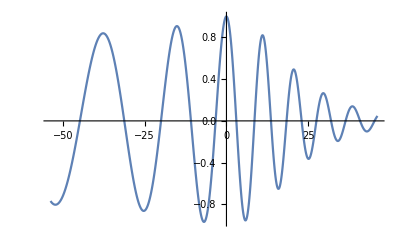

```mathematica
ListLinePlot[hpReSXS0746DataShift[[14700;;15700]]]
```

```mathematica
AmpSXS0746DataStrainNorm = AmpSXS0746DataStrain/MaxAmpSXS0746DataStrain;
```

```mathematica
AmpSXS0746DataShift=Transpose[{SXS0746DataTimeShift,AmpSXS0746DataStrainNorm }];
```

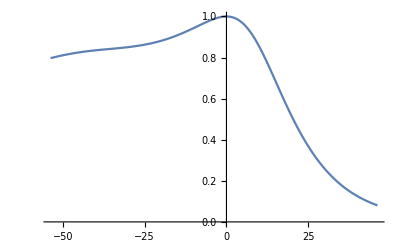

```mathematica
ListLinePlot[AmpSXS0746DataShift[[14700;;15700]]]
```

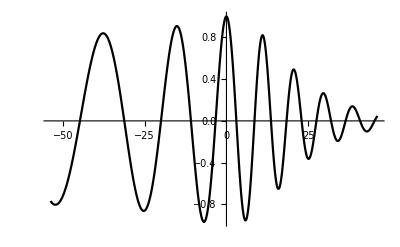

```mathematica
Show[Plot[Re[hBoB[t+th]]/MaxRehBoB,{t,-60,60}],
ListLinePlot[hpReSXS0746DataShift[[14700;;15700]],PlotStyle->Black],
PlotRange->All]
```

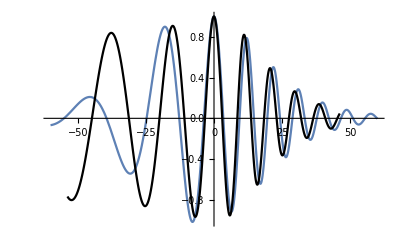

```mathematica
Show[Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-60,60}],
ListLinePlot[hpReSXS0746DataShift[[14700;;15700]],PlotStyle->Black],
PlotRange->All]
```

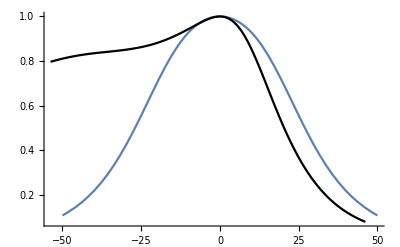

```mathematica
Show[Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0746DataShift[[14700;;15700]],PlotStyle->Black],PlotRange->All]
```

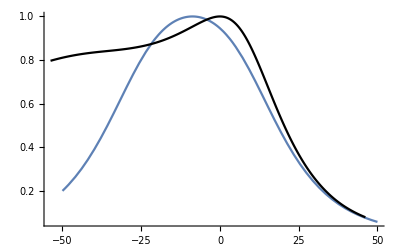

```mathematica
Show[Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0746DataShift[[14700;;15700]],PlotStyle->Black],PlotRange->All]
```

```mathematica
ArgSXS= Flatten[ArcTan[ImSXS0746DataStrainNorm/ReSXS0746DataStrainNorm]];
```

Function taken from https://community.wolfram.com/groups/-/m/t/1340126

```mathematica
Unwrap[lst_List]:=Unwrap[lst,2Pi] (*phase jumps of 2Pi is the default because of trigonometric funtions*)
Unwrap[lst_List,Δ_]:=Unwrap[lst,Δ,Scaled[0.5]] (*default tolerance is half the phase jump Δ*)
Unwrap[lst_List,Δ_,tolerance_]:=Module[{tol,jumps},tol=If[Head[tolerance]===Scaled,Δ tolerance[[1]],tolerance];
jumps=Differences[lst];
jumps=-Sign[jumps]Unitize[Chop[Abs[jumps],tol]];
jumps=Δ Prepend[Accumulate[jumps],0];
jumps+lst]
```

```mathematica
unwrapArgSXS=Unwrap[ArgSXS,3];
```

```mathematica
unwrapArgSXSFiltered=MeanFilter[unwrapArgSXS,100];
```

```mathematica
ϕSXS=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXS]}];
```

```mathematica
ϕSXSfiltered=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXSFiltered]}];
```

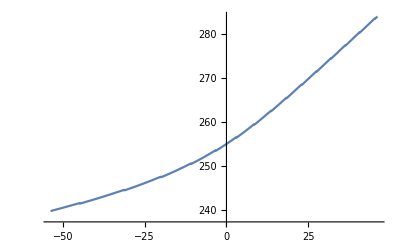

```mathematica
ListLinePlot[ϕSXS[[14700;;15700]]]
```

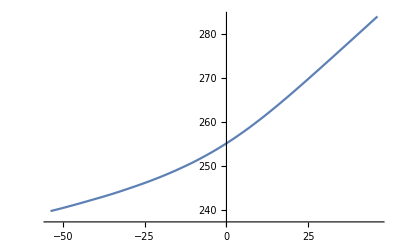

```mathematica
ListLinePlot[ϕSXSfiltered[[14700;;15700]]]
```

```mathematica
interpϕSXS=Interpolation[ϕSXS[[14700;;15700]],InterpolationOrder->4]
```

InterpolatingFunction[…]

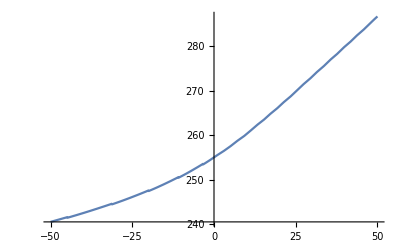

```mathematica
Show[Plot[interpϕSXS[t],{t,-50,50}]]
```

```mathematica
interpϕSXSfiltered=Interpolation[ϕSXSfiltered[[14700;;15700]],InterpolationOrder->4]
```

InterpolatingFunction[…]

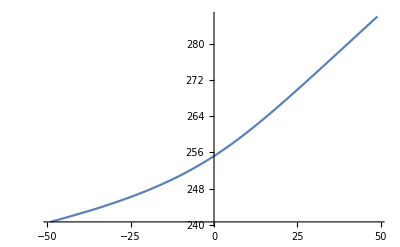

```mathematica
Show[Plot[interpϕSXSfiltered[t],{t,-49,49}]]
```

```mathematica
ΔϕSXSBoB =interpϕSXSfiltered[0]-Re[ϕBoB[tfBoB]]
```

244.254

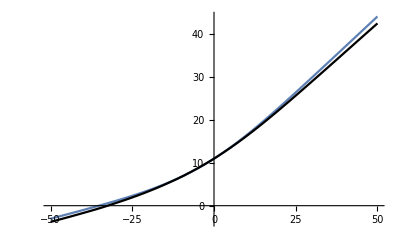

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

https://mathematica.stackexchange.com/questions/126302/how-to-get-a-smooth-derivative-graphic

```mathematica
dϕSXS=Differences[Last/@ϕSXSfiltered]
```

{0.0116856,0.0119525,0.0131447,0.0144768,0.0151795,0.0153317,0.0151634,16642,0.035514,0.0356431,0.0357708,0.0358962,0.0360181,0.0361361,0.0362491}
 |  |  |  |

```mathematica
dϕSXS=dϕSXS/Differences[First/@ϕSXSfiltered]
```

{0.0124237,0.0127075,0.013975,0.0153912,0.0161383,0.0163357,0.0161212,16642,0.355198,0.356489,0.357766,0.35902,0.36024,0.36142,0.36255}
 |  |  |  |

```mathematica
dϕSXSfiltered=MeanFilter[dϕSXS,100]
```

{0.0136955,0.0137791,0.0138635,0.0139456,0.0140325,0.0141175,0.0142032,16642,0.356843,0.354078,0.351265,0.348401,0.345483,0.342509,0.339475}
 |  |  |  |

```mathematica
{dϕSXS,dϕSXSfiltered}=Transpose[{Most[First/@ϕSXSfiltered],#}]&/@{dϕSXS,dϕSXSfiltered}
```

{{{-5200.06,0.0124237},{-5199.12,0.0127075},{-5198.18,0.013975},16650,{141.545,0.36024},{141.645,0.36142},{141.745,0.36255}},{1}}
 |  |  |  |

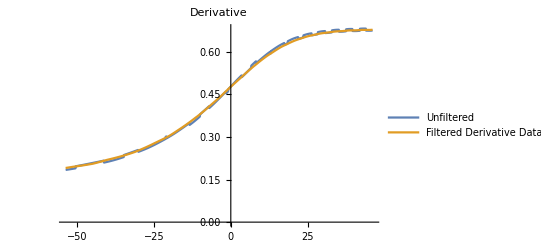

```mathematica
ListLinePlot[{dϕSXS[[14700;;15700]],dϕSXSfiltered[[14700;;15700]]},PlotStyle->{Thin,Thick},PlotLegends->{"Unfiltered","Filtered Derivative Data"},PlotLabel->"Derivative"]
```

```mathematica
interpωSXSfiltered=Interpolation[dϕSXSfiltered[[14700;;15700]],InterpolationOrder->4]
```

InterpolatingFunction[…]

```mathematica
interpωSXSfiltered[0]
```

0.476934

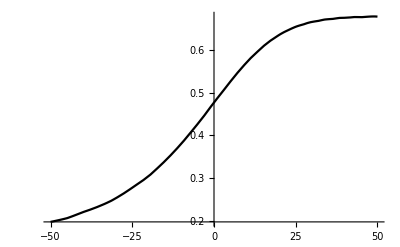

```mathematica
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->Black]
```

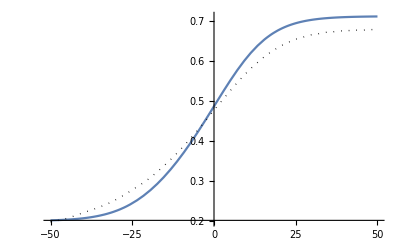

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

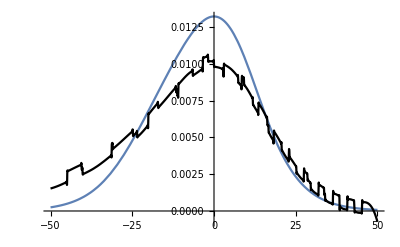

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered'[t],{t,-50,50},PlotStyle->{Black}],
PlotRange->All]
```

Plots for the paper

```mathematica
Show[Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0746DataShift[[14700;;15700]],PlotStyle->Black],PlotRange->All]
```

-Graphics-

```mathematica
Show[Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-60,60}],
ListLinePlot[hpReSXS0746DataShift[[14700;;15700]],PlotStyle->Black],
PlotRange->All]
```

-Graphics-

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

-Graphics-

Fig. 1

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

-Graphics-

```mathematica
interpωSXSfiltered[50]
```

InterpolatingFunction::dmval: Input value {50} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.678146

```mathematica
ωBoB[50+tfBoB]
```

0.711406

Light Ring Location

```mathematica
rLR[χf_] := 2 m(1 + Cos[2/3 ArcCos[-χf]])
```

```mathematica
rLRp=rLR[χf]/.{ m->1}
rLRm=rLR[-χf]/.{ m->1}
rLR = Mean[List[rLRp,rLRm]]
```

1.61351

3.89265

2.75308

```mathematica
rLR0=rLR[0]/.{ m->1}
```

2.75308[0]

```mathematica
rLR0Mf=rLR[0]/.{ m->Mf}
```

2.75308[0]

```mathematica
rLR[χf]/.{ m->Mf}
```

2.75308[0.880589]

```mathematica
Tc =Simplify[ 5/256 a^4/(m1 m2 m)]
```

(5 a^4)/(256 m m1 m2)

```mathematica
Tcp = Simplify[Tc/.{m->1,a->rLRp}]
Tcm = Simplify[Tc/.{m->1,a->rLRm}]
```

0.132377/(m1 m2)

4.48447/(m1 m2)

```mathematica
Mean[List[Tcp,Tcm]]
```

2.30842/(m1 m2)

```mathematica
TLR = Simplify[Tc/.{m->1,a->rLR}]
```

1.12203/(m1 m2)

```mathematica
TLRMf = Simplify[Tc/.{m->Mf,a->rLR0Mf}]
```

(0.0211758 (2.75308[0])^4)/(m1 m2)

```mathematica
TLR0 = Simplify[Tc/.{m->1,a->rLR0}]
```

(5 (2.75308[0])^4)/(256 m1 m2)

```mathematica
rLR0/6.328125
```

0.158025 2.75308[0]

```mathematica
tfBoB
```

-9.17457

```mathematica
tpBoB
```

-17.9107

```mathematica
ti-tfBoB
```

-35.1816

For the standard deviation plot

```mathematica
(*dataBoBr=Re[hBoB[t-trBoB/2]]/MaxAmpBoB;
dataBoB0=Re[hBoB[t-Δt0/2]]/MaxAmpBoB;
dataIRS=Re[hIRSΔ[t]]/MaxAmpIRS;
datamIRS=Re[-hIRS[t]]/MaxAmpIRS;
datamIRSΔ=Re[-hIRSΔ[t]]/MaxAmpIRS;*)
```

## Below is Tabulating for Python Plots

```mathematica
(*dt=0.01;*)
```

```mathematica
(*tArray=Table[t,{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBTab=Table[ωBoB[t+tfBoB],{t,-50,50,dt}];*)
```

```mathematica
(*ωIRSTab=Table[ωIRS[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωSXSTab=Table[interpωSXSfiltered[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBvsTimeTab=Partition[Riffle[tArray,ωBoBTab],2];*)
```

```mathematica
(*PrependTo[ωBoBvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωIRSvsTimeTab=Partition[Riffle[tArray,ωIRSTab],2];*)
```

```mathematica
(*PrependTo[ωIRSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωSXSvsTimeTab=Partition[Riffle[tArray,ωSXSTab],2];*)
```

```mathematica
(*PrependTo[ωSXSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wBoB.txt", ωBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wIRS.txt", ωIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wSXS.txt", ωSXSvsTimeTab]*)
```

```mathematica
(*ampBoBTab=Table[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50,50,dt}];*)
```

```mathematica
(*ampBoBvsTimeTab=Partition[Riffle[tArray,ampBoBTab],2];*)
```

```mathematica
(*PrependTo[ampBoBvsTimeTab, {"t(M)", "Amp"}];*)
```

```mathematica
(*ampIRSTab=Table[AmpIRS[t]/MaxAmpIRS,{t,-50,50,dt}];*)
```

```mathematica
(*ampIRSvsTimeTab=Partition[Riffle[tArray,ampIRSTab],2];*)
```

```mathematica
(*PrependTo[ampIRSvsTimeTab, {"t(M)", "Amp"}];*)
```

```mathematica
(*AmpSXS=PrependTo[AmpSXS0746DataShiftIRS[[16420;;17440]], {"t(M)", "Amp"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampBoB.txt", ampBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampIRS.txt", ampIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampSXS.txt", AmpSXS]*)
```

```mathematica
(*Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]*)
```

```mathematica
(*ϕBoBTab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];*)
```

```mathematica
(*ϕIRSTab=Table[ϕIRS+Δϕ,{t,-50,50,dt}];*)
```

```mathematica
(*ϕSXSTab=Table[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50,dt}];*)
```

```mathematica
(*ϕBoBvsTimeTab=Partition[Riffle[tArray,ϕBoBTab],2];*)
```

```mathematica
(*PrependTo[ϕBoBvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*ϕIRSvsTimeTab=Partition[Riffle[tArray,ϕIRSTab],2];*)
```

```mathematica
(*PrependTo[ϕIRSvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*ϕSXSvsTimeTab=Partition[Riffle[tArray,ϕSXSTab],2];*)
```

```mathematica
(*PrependTo[ϕSXSvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiBoB.txt", ϕBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiIRS.txt", ϕIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiSXS.txt", ϕSXSvsTimeTab]*)
```

```mathematica
(*"dropbox/dillon/2022/Data/phiSXS.txt"*)
```

```mathematica
(*Show[Plot[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[hpReSXS0746DataShift[[16420;;17440]],PlotStyle->Black],
PlotRange->All]*)
```

```mathematica
(*hBoBTab=Table[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-50,50,dt}];*)
```

```mathematica
(*hIRSTab=Table[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50,dt}];*)
```

```mathematica
(*hBoBvsTimeTab=Partition[Riffle[tArray,hBoBTab],2];*)
```

```mathematica
(*PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];*)
```

```mathematica
(*hIRSvsTimeTab=Partition[Riffle[tArray,hIRSTab],2];*)
```

```mathematica
(*PrependTo[hIRSvsTimeTab, {"t(M)", "h(t)"}];*)
```

```mathematica
(*hSXS=PrependTo[hpReSXS0746DataShift[[16420;;17440]], {"t(M)", "h(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hBoB.txt", hBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hIRS.txt", hIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hSXS.txt", hSXS]*)
```